```mathematica
data=ReadList["C:\\Users\\Christopher Plumberg\\Downloads\\slice_T500.dat",Real];
data=ArrayReshape[data,{Length[data]/11,11}][[;;,{2,3,4,7,8,9,10}]];
data2=ReadList["C:\\Users\\Christopher Plumberg\\Downloads\\sparse_grid.dat",Real];
data2=ArrayReshape[data2,{Length[data2]/11,11}][[;;,{2,3,4,7,8,9,10}]];
(*data=Select[data[[;;,{2,3,4,10}]],#[[2]]==0&][[;;,{1,3,4}]];*)
```

```mathematica
ℏc=197327/1000;
data[[;;,{4,5,6}]]*=30^3/ℏc^3;
data[[;;,7]]*=10^-3 30^4/ℏc^3;
data2[[;;,{4,5,6}]]*=30^3/ℏc^3;
data2[[;;,7]]*=10^-3 30^4/ℏc^3;
```

```mathematica
data2[[;;;;5^6]]//Length
```

43

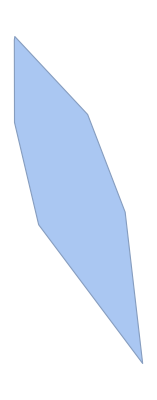

{{-0.0711625,-0.226038},{-0.146324,0.0915186},{0.197695,-0.186767},{0.0811001,0.116157},{-0.146848,0.347193},{-0.145342,0.358041},{0.252159,-0.656447}}

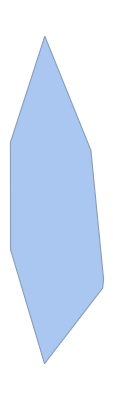

{{-0.00104515,-0.699143},{-0.000842006,-0.699638},{2.25595×10^-6,-0.699401},{1.17371×10^-6,0.69891},{0.000865829,0.699158},{0.00107095,0.698873},{-0.146324,-0.21223},{0.197695,0.212596},{-0.146848,0.245855},{0.248111,-0.377162},{0.252159,-0.340109}}

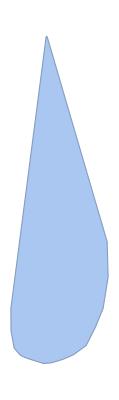

{{-0.00203155,1.32428},{0.00223829,1.32278},{0.00206659,1.32315},{-0.146324,0.125315},{-0.133347,0.0529229},{-0.0132689,-0.00949433},{-0.146848,0.21419},{0.248111,0.487258},{0.019177,-0.00708046},{-0.0823212,0.0122426},{0.110327,0.02643},{-0.106883,0.0231424},{0.0869752,0.0159123},{0.252159,0.343902},{0.162401,0.0641072},{0.0670627,0.00760747},{0.231604,0.215456},{0.200546,0.139642}}

```mathematica
ConvexHullMesh[data2[[;;;;10,{4,5}]]]
%//MeshCoordinates
ConvexHullMesh[data2[[;;;;10,{4,6}]]]
%//MeshCoordinates
ConvexHullMesh[data2[[;;;;10,{4,7}]]]
%//MeshCoordinates
```

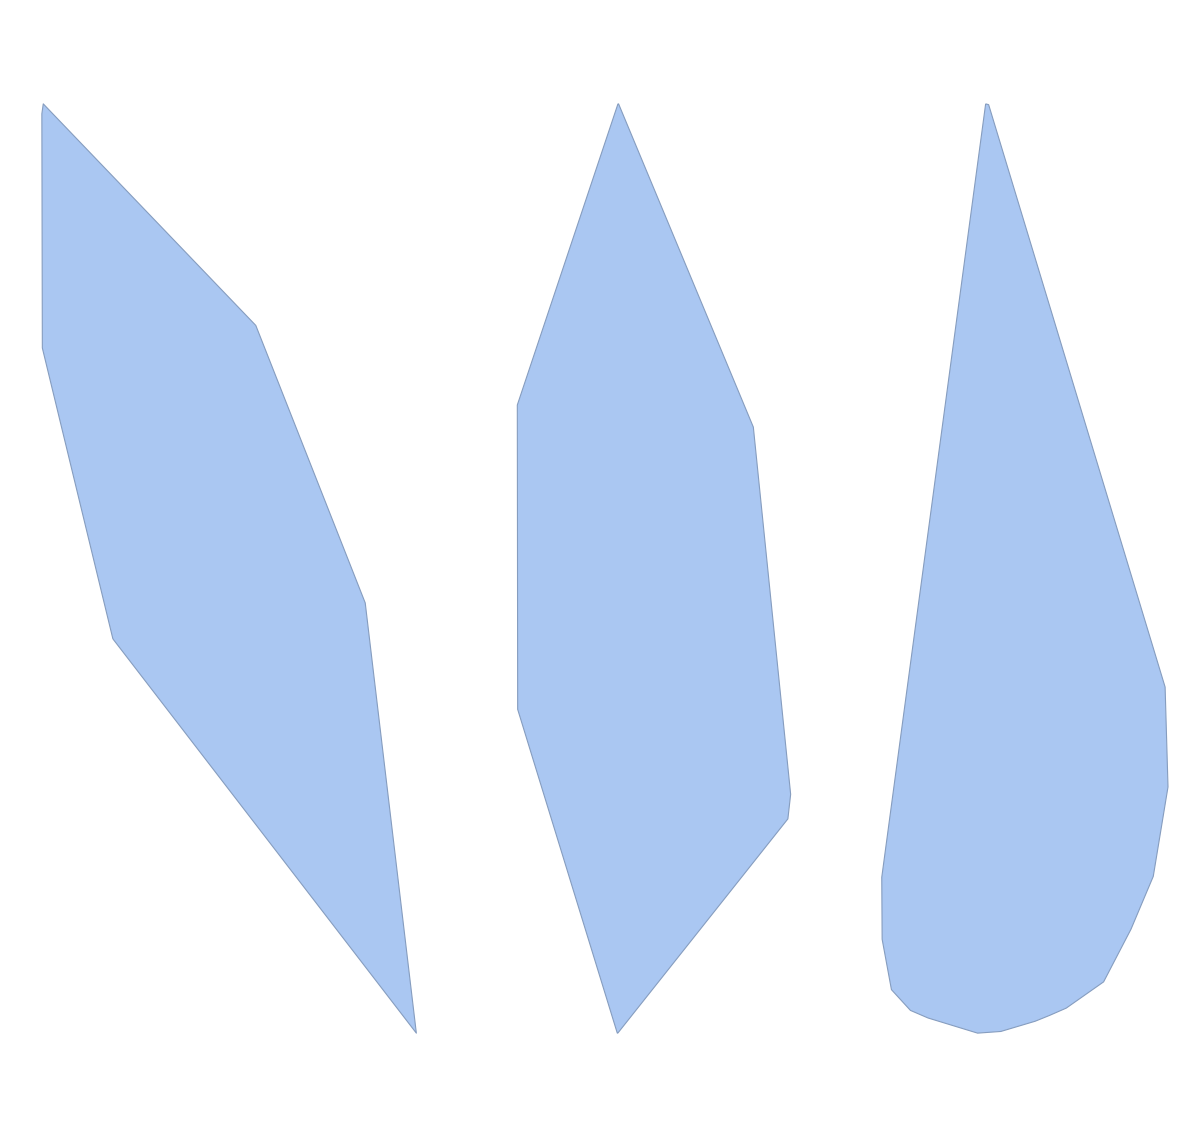

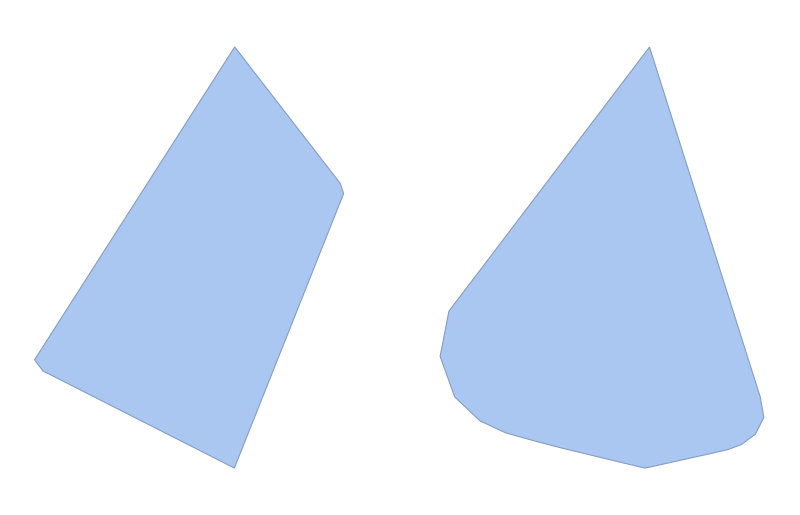

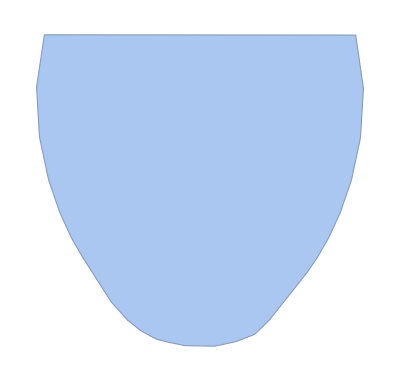

```mathematica
data3=data2[[;;;;10]];
GraphicsRow[{ConvexHullMesh[data3[[;;,{4,5}]]],ConvexHullMesh[data3[[;;,{4,6}]]],ConvexHullMesh[data3[[;;,{4,7}]]]}]
GraphicsRow[{ConvexHullMesh[data3[[;;,{5,6}]]],ConvexHullMesh[data3[[;;,{5,7}]]]}]
GraphicsRow[{ConvexHullMesh[data3[[;;,{6,7}]]]}]
```

```mathematica
DelaunayMesh[data[[;;,{4,7}]]]
```

-Graphics-

-Graphics3D-

{40,3}

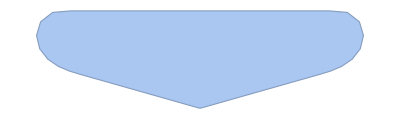

{20,2}

```mathematica
ConvexHullMesh[data[[;;,{4,5,6}]]]
mc=%//MeshCoordinates;
mc//Dimensions
ConvexHullMesh[data2[[;;,{4,7}]]]
mc2=%//MeshCoordinates;
mc2//Dimensions
```

```mathematica
mc==mc2//FullSimplify
Norm/@mc
```

True

{0.0183114,0.0136231,0.0143058,0.0150542,0.0158706,0.00417455,0.0194747,0.0207096,0.0220128,0.0233867,0.0248335,0.0263556,0.0279553,0.0296349,0.0313967,0.0332432,0.0351765,0.0371992,0.0393136,0.041522,0.041522,0.0393136,0.0371992,0.0351765,0.0332432,0.0313967,0.0296349,0.0279553,0.0263556,0.0248335,0.0233867,0.0220128,0.0207096,0.0194747,0.00417455,0.0158706,0.0150542,0.0143058,0.0136231,0.0183114}

```mathematica
n=4;
model=Sum[Subscript[a, i,j,k](μB/1200)^i(μS/1200)^j(μQ/1200)^k,{i,0,n},{j,0,n},{k,0,n}];
cfs=Flatten[Table[{Subscript[a, i,j,k],1},{i,0,n},{j,0,n},{k,0,n}],2];
vars={μB,μS,μQ};
fit=FindFit[data,model,cfs,vars]//Chop
```

{a_(0,0,0)→0.169847,a_(0,0,1)→0,a_(0,0,2)→0.0742657,a_(0,0,3)→0,a_(0,0,4)→2.4668,a_(0,1,0)→0,a_(0,1,1)→-0.356068,a_(0,1,2)→0,a_(0,1,3)→6.2692,a_(0,1,4)→0,a_(0,2,0)→90.0982,a_(0,2,1)→0,a_(0,2,2)→7.2522,a_(0,2,3)→0,a_(0,2,4)→0,a_(0,3,0)→0,a_(0,3,1)→5.00317,a_(0,3,2)→0,a_(0,3,3)→0,a_(0,3,4)→0,a_(0,4,0)→12437.9,a_(0,4,1)→0,a_(0,4,2)→0,a_(0,4,3)→0,a_(0,4,4)→0,a_(1,0,0)→0,a_(1,0,1)→-0.166672,a_(1,0,2)→0,a_(1,0,3)→-0.0000820563,a_(1,0,4)→0,a_(1,1,0)→0.0207612,a_(1,1,1)→0,a_(1,1,2)→-0.0541875,a_(1,1,3)→0,a_(1,1,4)→0,a_(1,2,0)→0,a_(1,2,1)→-0.0685569,a_(1,2,2)→0,a_(1,2,3)→0,a_(1,2,4)→0,a_(1,3,0)→-0.00467445,a_(1,3,1)→0,a_(1,3,2)→0,a_(1,3,3)→0,a_(1,3,4)→0,a_(1,4,0)→0,a_(1,4,1)→0,a_(1,4,2)→0,a_(1,4,3)→0,a_(1,4,4)→-1.2514×10^-10,a_(2,0,0)→6.96116×10^-9,a_(2,0,1)→0,a_(2,0,2)→-0.00118176,a_(2,0,3)→0,a_(2,0,4)→-1.50614×10^-10,a_(2,1,0)→0,a_(2,1,1)→-3.55432,a_(2,1,2)→-1.01606×10^-10,a_(2,1,3)→0,a_(2,1,4)→1.00602×10^-10,a_(2,2,0)→0.00276945,a_(2,2,1)→0,a_(2,2,2)→-7.53493×10^-10,a_(2,2,3)→1.20987×10^-10,a_(2,2,4)→6.96369×10^-10,a_(2,3,0)→0,a_(2,3,1)→0,a_(2,3,2)→1.73938×10^-10,a_(2,3,3)→0,a_(2,3,4)→-1.74907×10^-10,a_(2,4,0)→-1.22484×10^-10,a_(2,4,1)→0,a_(2,4,2)→5.5031×10^-10,a_(2,4,3)→-1.31781×10^-10,a_(2,4,4)→-4.8139×10^-10,a_(3,0,0)→0,a_(3,0,1)→-0.0156577,a_(3,0,2)→0,a_(3,0,3)→0,a_(3,0,4)→0,a_(3,1,0)→17.8434,a_(3,1,1)→0,a_(3,1,2)→0,a_(3,1,3)→0,a_(3,1,4)→0,a_(3,2,0)→0,a_(3,2,1)→0,a_(3,2,2)→1.4381×10^-10,a_(3,2,3)→0,a_(3,2,4)→-1.44141×10^-10,a_(3,3,0)→0,a_(3,3,1)→0,a_(3,3,2)→1.06686×10^-10,a_(3,3,3)→0,a_(3,3,4)→-1.18661×10^-10,a_(3,4,0)→0,a_(3,4,1)→0,a_(3,4,2)→-1.73063×10^-10,a_(3,4,3)→-1.00718×10^-10,a_(3,4,4)→2.38709×10^-10,a_(4,0,0)→-1.0081,a_(4,0,1)→0,a_(4,0,2)→0,a_(4,0,3)→0,a_(4,0,4)→1.32107×10^-10,a_(4,1,0)→0,a_(4,1,1)→0,a_(4,1,2)→1.18958×10^-10,a_(4,1,3)→0,a_(4,1,4)→-1.62166×10^-10,a_(4,2,0)→-1.47902×10^-10,a_(4,2,1)→0,a_(4,2,2)→7.67401×10^-10,a_(4,2,3)→-1.52808×10^-10,a_(4,2,4)→-6.9868×10^-10,a_(4,3,0)→0,a_(4,3,1)→0,a_(4,3,2)→-2.23056×10^-10,a_(4,3,3)→0,a_(4,3,4)→2.86952×10^-10,a_(4,4,0)→1.47401×10^-10,a_(4,4,1)→-1.21024×10^-10,a_(4,4,2)→-5.30298×10^-10,a_(4,4,3)→2.00462×10^-10,a_(4,4,4)→3.79377×10^-10}

```mathematica
modelfit=model/.fit;
modelpts=(modelfit/.{μB->#[[1]],μS->#[[2]],μQ->#[[3]]})&/@data;
√((data[[;;,4]]-modelpts)^2//Mean)
```

2.25743×10^-11